# Moran indices for experimental data

## Supplementary material for Fischer et al "The salt-and-pepper pattern in mouse blastocysts is compatible with signalling beyond the nearest neighbours."

## Initialisation

```mathematica
<<(FileNameJoin[{NotebookDirectory[],"CellNucleiSegmentation_v8.m"}]) (*code from Schmitz et al. Scientific Reports 2017*)
```

```mathematica
<<(FileNameJoin[{baseFolder,"neighbourAnaFunctions_v2.m"}])(*code from Fischer et al. PLOS One 2020 and extensions*)
```

Get::stream: FileNameJoin[{baseFolder,neighbourAnaFunctions_v2.m}] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

$Failed

```mathematica
fontOption="Arial";
```

```mathematica
colour3[i_]:=Join[{Darker[Gray]},(ColorData[16]/@{3,6,4})][[i]]
```

```mathematica
plotMeanStdLighter[xValues_,yValues_,smooth_,xLabel_,yLabel_,colour_]:=
Show[Table[ListLinePlot[{Transpose[{xValues[[i]],MeanFilter[#[[All,1]]+#[[All,2]],smooth]}],
Transpose[{xValues[[i]],MeanFilter[#[[All,1]]-#[[All,2]],smooth]}]}&@yValues[[i]],PlotRange->{0,All},
PlotStyle->{Directive[Opacity[0.5],Lighter[colour[i],0.7]],Directive[Opacity[0.5],Lighter[colour[i],0.7]]},Filling->1->{2},FillingStyle->Directive[Opacity[0.5],Lighter[colour[i],0.5]],Frame->{True,True,None,None},FrameStyle->Directive[Black,(*Thick,*)FontFamily->fontOption,14],(*TicksStyle->Thick,*)FrameLabel->{xLabel,yLabel}],{i,1,Length[xValues]}],
ListLinePlot[Table[Transpose[{xValues[[i]],MeanFilter[#[[All,1]],smooth]}]&@yValues[[i]],{i,1,Length[xValues]}],
PlotRange->{0,All},PlotStyle->Transpose[{ConstantArray[Thickness[0.007],Length[xValues]],Table[colour[i],{i,1,Length[xValues]}]}],Frame->{True,True,None,None},FrameStyle->Directive[Black,FontFamily->fontOption,14],FrameLabel->{xLabel,yLabel}]]
```

```mathematica
populationsColours={Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]};
```

## Moran index of data

```mathematica
allFolders={"SMD_2020_NG6","SMD_2021_NG6G4","JLG_2021_NG6","NS_2016_NG6","NS_2020_NG6","NS_2020_NRatG6Rb","NS_2020_NRatG6Gt"};
```

```mathematica
finalFNames=Flatten[FileNames["*FinalData.mx",FileNameJoin[{StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\"<>#)],"EmbryoFeatures"}]]&/@allFolders];
```

```mathematica
Length[finalFNames]
```

738

this also includes embryos at stage 3.0 which will be discarded below

```mathematica
data=Import[#]&/@finalFNames;
```

```mathematica
data[[1]]//Keys
```

{NucleiFeatures,GlobalFeatures,Staging}

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
nucleiFeatures[[1,1]]//Keys
```

{Inlier/Outlier,EmbryoId,CellID,Size,TE/ICM,Centroid,Dapi-Avg,Dapi-Sum,Brightfield-Avg,Brightfield-Sum,Gata6-Avg,Gata6-Sum,ABC-Avg,ABC-Sum,Nanog-Avg,Nanog-Sum,Dapi-AvgLnCorr,Nanog-AvgLnCorr,Gata6-AvgLnCorr,SurfaceDistance,SurfaceNearest,PCGNeighborCount,PCGClusteringCoefficient,PCGMinNeighborDistance,PCGMaxNeighborDistance,PCGMeanNeighborDistance,PCGStandardDeviationNeighborDistance,DCGNeighborCount,DCGClusteringCoefficient,DCGMinNeighborDistance,DCGMaxNeighborDistance,DCGMeanNeighborDistance,DCGStandardDeviationNeighborDistance,Dapi-AvgNorm,Brightfield-AvgNorm,Gata6-AvgNorm,ABC-AvgNorm,Nanog-AvgNorm,Dapi-AvgNorm,Nanog-AvgNorm,Gata6-AvgNorm,Nanog-AvgShifted,Gata6-AvgShifted,Quadrant}

```mathematica
staging=("Staging"/.data);
```

```mathematica
dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.data))}];
```

Form Simon’s thesis:

-Graphics-

hence, if an embryo has only cells of one type, the denominator is zero. i.e. we need to exclude all embryos that have only cells of one type (positive or negative)

```mathematica
moranValues=MapThread[Rule,{{"Stage","Embryo","Experiment","N+-Moran","N-AvgShifted-Moran","G6+-Moran","G6-AvgShifted-Moran"},#}]&/@(Table[Join[staging[[i,{3,2,1}]],{({valuesN,weights}=prepareDataMoran[nucleiFeatures[[i]],dcgGraphs[[i,2]],"N+"];If [Length[DeleteDuplicates[valuesN]]>1,calcMoranI[valuesN,weights],"only one cell type"]),
(nucleiFeaturesICM=Select[nucleiFeatures[[i]],("TE/ICM"/.#)≠"TE"&];calcMoranI["Nanog-AvgShifted"/.nucleiFeaturesICM,weights]),
({valuesG6,weights}=prepareDataMoran[nucleiFeatures[[i]],dcgGraphs[[i,2]],"G6+"];If [Length[DeleteDuplicates[valuesG6]]>1,calcMoranI[valuesG6,weights],"only one cell type"]),calcMoranI["Gata6-AvgShifted"/.nucleiFeaturesICM,weights]}],{i,1,Length[nucleiFeatures]}]);
```

number of embryos discarded for NANOG

```mathematica
Length[Cases["N+-Moran"/.moranValues,"only one cell type"]]
```

63

number of embryos discarded for GATA6

```mathematica
Length[Cases["G6+-Moran"/.moranValues,"only one cell type"]]
```

100

```mathematica
Length[Cases["G6+-Moran"/.moranValues,Except["only one cell type"]]]
```

638

```mathematica
moranValuesByStage=Table[Select[moranValues,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
Length/@moranValuesByStage
```

{326,218,177}

```mathematica
Total[Length/@moranValuesByStage]
```

721

```mathematica
Length[Cases["N+-Moran"/.#,"only one cell type"]]&/@moranValuesByStage
```

{51,2,2}

```mathematica
Length[Cases["G6+-Moran"/.#,"only one cell type"]]&/@moranValuesByStage
```

{64,19,6}

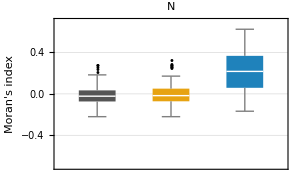
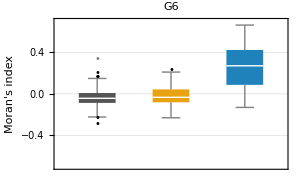

```mathematica
plotMoran=Row[Table[BoxWhiskerChart[Cases[#,Except["only one cell type"]]&/@(i/.moranValuesByStage),"Outliers",ChartLabels->{{"early","mid","late"},None},PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@StringDelete[i,"+-Moran"],ImageSize->300,PlotRange->{-0.7,0.7},FrameLabel-> {None,"Moran's index"},FrameStyle->Directive[Black,20],ChartStyle->(colour3[#]&/@{1,2,3}),PlotTheme->"Detailed"],{i,{"N+-Moran","G6+-Moran"}}],"     "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","moran_Data.png"}],plotMoran]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"ResultsAll","moranValuesByStage.mx"}],moranValuesByStage]
```